```mathematica
SizedDots[n_]:= Table[ Directive[PointSize[0.05*(n+1-i)/n],Hue[i/n]],{i,n}]
```

# Henon Map Manifolds

## Basic Map and Attractor

The Henon map has simple derivatives etc.

```mathematica
F[a_,b_][{x_,y_}]:={1- a x^2 + y, b x}
DF[a_,b_][{x_,y_}]:={{-2 a x,1},{b,0}}
```

The inverse map is easily computed

```mathematica
Simplify[Solve[F[a,b][{X,Y}]=={x,y},{X,Y}]]
```

{{X→y/b,Y→-1+x+(a y^2)/b^2}}

We put it in a function with an “obvious” name.

```mathematica
FInv[a_,b_][{x_,y_}]:= {y/b, -1+x + a y^2/b^2}
```

```mathematica
FInv[a,b][F[a,b][{x,y}]]
```

{x,y}

Our target is to start to understand and plot the stable and unstable manifolds of the Fixed Points

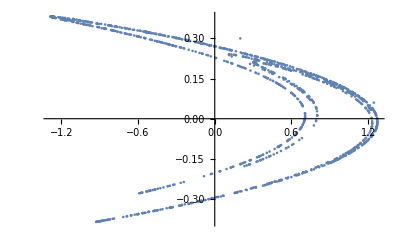

```mathematica
{a,b}={1.4,0.3};
Pic=ListPlot[NestList[F[a,b],{0.2,0.3},1234]]
```

## Fixed Points

The Henon map has two Fixed Points

```mathematica
Clear[x,y,a,b]
{x,y}/.Solve[F[a,b][{x,y}]=={x,y},{x,y}]
```

{{-(1-b+√(1+4 a-2 b+b^2))/(2 a),1/2 (-b/a+b^2/a-(b √(1+4 a-2 b+b^2))/a)},{(-1+b+√(1+4 a-2 b+b^2))/(2 a),1/2 (-b/a+b^2/a+(b √(1+4 a-2 b+b^2))/a)}}

As always we might as well make a function

```mathematica
FixedPts[a_,b_]:={
{-(1-b+√(1+4 a-2 b+b^2))/(2 a),1/2 (-b/a+b^2/a-(b √(1+4 a-2 b+b^2))/a)},{(-1+b+√(1+4 a-2 b+b^2))/(2 a),1/2 (-b/a+b^2/a+(b √(1+4 a-2 b+b^2))/a)}}
```

We should test

```mathematica
Clear[a,b]
{p1,p2}=FixedPts[a,b];
Simplify[{p1-F[a,b][p1],p2-F[a,b][p2]}]
```

{{0,0},{0,0}}

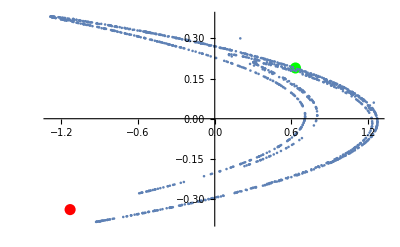

```mathematica
{a,b}={1.4,0.3};
Pic=ListPlot[NestList[F[a,b],{0.2,0.3},1234],
Prolog->{PointSize[0.02],
{Red,Point[FixedPts[a,b]⟦1⟧]},
{Green,Point[FixedPts[a,b]⟦2⟧]}}]
```

Lets look at the eigenvalues of the fixed points for the standard parameters a=1.4 and b=0.3

```mathematica
{a,b}={1.4,0.3};
{p1,p2}=FixedPts[a,b];
Eigenvalues[DF[a,b][p1]]
Eigenvalues[DF[a,b][p2]]
```

{3.25982,-0.0920296}

{-1.92374,0.155946}

Both fixed points have a bit that gets sucked in and a bit that gets spat out.  The eigenvectors show how these line up.

{{-1.92374,0.155946},{{-0.988058,0.154084},{-0.461228,-0.887282}}}

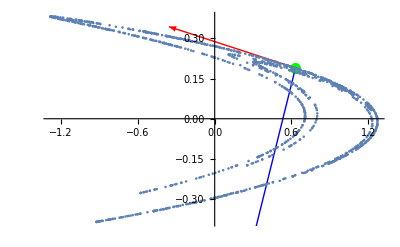

```mathematica
p=p2;
{λs,vs}=Eigensystem[DF[a,b][p]]
ListPlot[NestList[F[a,b],{0.2,0.2},1234],
Prolog->{Green, PointSize[0.02],Point[p],
{Red, Arrow[{p,p+vs⟦1⟧}]},
{Blue,Arrow[{p,p+vs⟦2⟧}]}
}]
```

We should see how this works at the other fixed point!

{{3.25982,-0.0920296},{{0.995792,0.0916423},{-0.293276,0.956028}}}

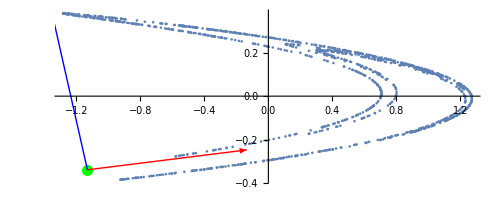

```mathematica
p=p1;
{λs,vs}=Eigensystem[DF[a,b][p]]
ListPlot[NestList[F[a,b],{0.2,0.2},1234],
AspectRatio->Automatic,
Prolog->{Green, PointSize[0.02],Point[p],
{Red,Arrow[{p,p+vs⟦1⟧}]},
{Blue,Arrow[{p,p+vs⟦2⟧}]}
}]
```

## Manifolds: Definitions

The formal definition of the stable manifold of a hyperbolic fixed point p of a map F:ℝ^m→ℝ^m is easy to state
	S_p={q∈ℝ^m:q->p under the map F}
For an invertible map F the definition of the unstable manifold is just about as simple
	U_p={q∈ℝ^m:q->p under the map F^-1}
Both definitions hide quite a lot of detail.

## Manifolds: Visualization Idea

The only easy point on these manifolds is the fixed point!

To sketch an unstable manifolds we can start out from the fixed point and see where we go under F.

Of course, we can not start out at the fixed point we need to start out near the fixed point!

Not all directions are created equal.

Near the fixed point F is well approximated by its linearization which is basically the Jacobian/Derivative Matrix.

To sketch a stable manifolds we can start out from the fixed point and see where we go under F^-1.

Of course, we can not start out at the fixed point we need to start out near the fixed point!

Not all directions are created equal.

Near the fixed point F^-1 is well approximated by its linearization which is basically the inverse of the Jacobian/Derivative Matrix.

## Manifolds: For Linear Maps

Lets compute these manifolds for the linear map
	F[{x,y}]=A.(x
y)
where A is a 2 by 2 real matrix with real eigenvalues 0<λ_1<1<λ_2.  Note F has a single fixed point at the zero vector.  Writing v_1 and v_2 for the matching eigenvectors i.e. A.v_1=λ_1 v_1 and A.v_2=λ_2 v_2 we see that 
	F^(∘n)[α v_1]=α λ_1^n v_1  and F^(∘n)[β v_2]=β λ_2^n v_2 and
	 (F^-1)^(∘n)[α v_1]=α λ_1^-n v_1  and (F^-1)^(∘n)[β v_2]=β λ_2^-n v_2
Since 0<λ_1<1  we have λ_1^n→0  and since λ_2>1 we have λ_2^-n->0.   Almost by definition the manifolds are the lines in the eigen value directions.

Lets practice our sketchy manifold plan on a linear example 
	(x
y)→A.(x
y)	
and see if it shows us any tricky things!  There is a single fixed point at OverVector[0].

```mathematica
A={{2,0.5},{0.5,0.5}};
F[{x_,y_}]:= A.{x,y}
FP={0,0};
{{λ2,λ1},{v2,v1}}= Eigensystem[A];
{λ1,λ2}
ϵ=0.5; MaxIter=234;
ListPlot[{
NestList[F, 0.05{1,1}, MaxIter],
NestList[F, 0.05{-1,1}, MaxIter],
NestList[F, 0.1v1+{0.0000001,0}, MaxIter]},
Epilog-> {PointSize[0.02],Point[FP],
{Red,Arrow[{FP+ϵ v1,FP}],Arrow[{FP-ϵ v1,FP}]},
{Blue, Arrow[{FP,FP+ϵ v2}],Arrow[{FP,FP-ϵ v2}]}
},
Frame->True,
PlotRange->0.5{{-1.,1},{-1,1}}]
```

{0.348612,2.15139}

-Graphics-

```mathematica
NestList[F, 0.1v1, MaxIter]
```

{{0.0289784,-0.0957092},{0.0101022,-0.0333654},{0.00352176,-0.0116316},{0.00122773,-0.00405491},{0.000428001,-0.00141359},{0.000149206,-0.000492795},{0.0000520152,-0.000171794},{0.0000181331,-0.0000598896},{6.32143×10^-6,-0.0000208783},{2.20373×10^-6,-7.27841×10^-6},{7.68246×10^-7,-2.53734×10^-6},{2.6782×10^-7,-8.84549×10^-7},{9.33652×10^-8,-3.08365×10^-7}}

## Manifolds: Visualization Implementation Plan

The only easy point on these manifolds is the fixed point!

To sketch an unstable manifolds we can start out from the fixed point and see where we go under F.

Expand a tiny piece of the local unstable manifold using F.

To sketch a stable manifolds we can start out from the fixed point and see where we go under F^-1.

Expand a tiny piece of the local stable manifold using F^-1.

These things start wiggling really fast! The distortions grow exponentially.  Which does not mean what most folks think it means! https://www.youtube.com/watch?v=dTRKCXC0JFg